```mathematica
This file exports 2 things.
1)  experiemental [MP]+[MPR] vs time (converted from the fluoroscence data)
2) The initial [BT] concentrations that are extracted from the experimental data
```

Exporting concBT and normalized [MPR] + [PR] for : B1/M1P27-5

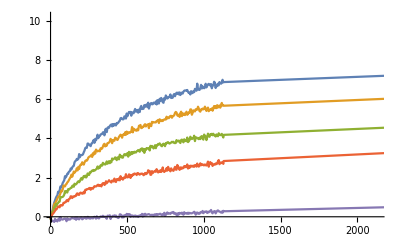

Exporting concBT and normalized [MPR] + [PR] for : B2/M2P27-5

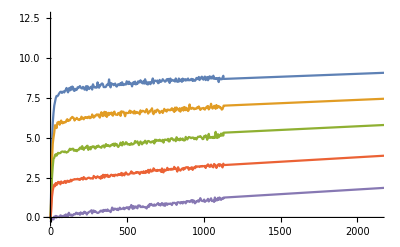

Exporting concBT and normalized [MPR] + [PR] for : B3/M3P27-5

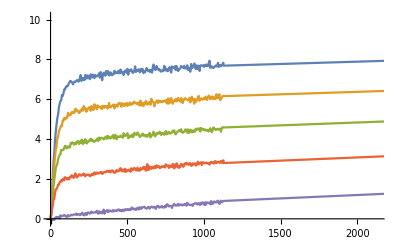

```mathematica
(*dnewfltem will store fluoroscent signal from Alexa,
dnewfl will store fluoroscent signal from Cy3*)
(*The protocol for extracting data is similar to the one found in Lock_opening_final.nb*)

SetDirectory[ParentDirectory[NotebookDirectory[]]];
SetDirectory["3. Template recovery"];
files={"20211222 TR plate1.xlsx","20220119 TR plate2.xlsx","20220124 TR plate3.xlsx","20220125 TR plate4.xlsx"}; (*Order of files:P29-5, P28-5, P27-5, P27-4*)
satred=Import["Sat_red.wl"];
(*Change these variables*)
tend=800;(*final time of interest*)

For[fname=3,fname<=3(*Length[files]*),fname++,
fname;(*File index of interest*)
Po=50;(*proofreader concentration*)
Btype=1;(*1 means B1, 2 means B1a, 3 means B1b*)
printall=0;
w1=1;(*Changes weight on point before injection*)
w2=0;(*changes weight on point after injection*)

(*These variables remain constant more or less*)
injinfo=0;(*If injinfo =0, use conc before injection and time as avg of before and after, else use conc after injection and time as after injection*)
forward=1;(*1 if reaction forward going BP+RQ->BPR+Q, 0 otherwise*)
skip=0;(*skip timesteps after injection or not*)
X1corr=0;(*If 1, subtract sample X1 readings, else not*)
FRQ=691.03;(*Fl Alexa density of RQ*)
FBPR=8261.9;(*Fl Alexa density of BPR*)
FBP=8993;(*Fl Cy3 of BP*)
FC3BPR=8178.8;(*Cy3 value for BPR*)

data=Import[files[[fname]],{"Sheets","Table All Cycles"}];

(*Extract relevant data*)
For[i=1,i<=Length[data],i++,
If[data[[i]][[1]]=="Content",Break[]]];
data=data[[i;;,2;;]];
(* 
data is as follows;
Time[min] Sample X1 Sample X2 Sample X3 Sample X4 Sample X5 Sample X6...
0 8983 9948 9248 9686 9373 9062
0.53 8696 9316 10039 9228 9138 9028
0.92 8647 9180 9539 9510 9125 9608
1.3 8820 9767 9968 9609 9353 9411
....
...*)

(*Stores the legends in this variable*)
samplename=data[[1]][[2;;]];
legend={};(*will remove samples of insignificance from samplename array and be used as the legend list*)
For[i=1,i<=Length[samplename],i++,
If[samplename[[i]]=="Control C1"||samplename[[i]]=="Control C2"||samplename[[i]]=="Control C3"||samplename[[i]]=="Positive control P"||samplename[[i]]=="Negative control N",,
AppendTo[legend,samplename[[i]]];
]]

(*Extract column number of Poitive and Negative control (and extra conrols if exist). Also extract column number of Sample X1 and row number of Alexa and Cy3 Injection*);

For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C3"||data[[1]][[i]]=="Negative control N",Break[]]];iC3=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C2",Break[]]];iC2=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Control C1"||data[[1]][[i]]=="Positive control P",Break[]]];iC1=i;
For[i=1,i<=Length[data[[1]]],i++,If[data[[1]][[i]]=="Sample X1",Break[]]];iS0=i;
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="Inj.",c++;If[c==2,Break[]]]];inj0=i;(*first injection row number*)
c=1;For[i=1,i<=Length[data],i++,If[data[[i]][[2]]=="Inj.",c++;If[c==3,Break[]]]];inj=i;(*second injection row number*)
If[printall==1,Print["Row number of Cy3 injection:", inj]];

(*Functions defined for further data processing*)
(*The "cut" function only takes data upto a certain time point*)
f[x_]:=0;
cut[x_,t_]:=(For[i=1,i<=Length[x[[1]]],i++,If[x[[1]][[i]][[1]]>t,Break[]];];ret={};
For[j=1,j<=Length[x],j++,AppendTo[ret,x[[j]][[1;;Min[i,Length[x[[j]]]]]]]];Return[ret];);

(**************************************************************************************)
dnew=Array[f,Length[data[[1]]]-1];(*Stoes raw Alexa data*)
dnewtem=dnew;(*Stores raw Cy3 data*)
dnewfl=Array[f,Length[data[[1]]]-4];(*Stores Alexa normalized data*)
dnewfltem=dnewfl(*Stores Cy3 normalized data*);
(***************************************************************************************)

(*Create a concentration array where each element stores a table of {time,fluoroscence} after injection for the different samples including +ve and -ve controls*)
For[i=2,i<=Length[data[[1]]],i++,dnew[[i-1]]=data[[2;;,{1,i}]];]

(*Find the second Inj. point and save the row number where the time before 2nd Inj. is 0. *);
c=1;
For[i=1,i<=Length[dnew[[1]]],i++,
If[c==3,Break[]];
If[dnew[[1]][[i]][[2]]=="Inj.",c++];
If[c==3,For[j=i-1,j>=1,j--,If[dnew[[1]][[j]][[1]]==0.,save=j;Break[];]]]
];
inj=inj-save+1;

(*Extract Alexa signal and define time, conc at the injection point*)
For[i=2,i<=Length[data[[1]]],i++,
dnew[[i-1]]=data[[2;;save,{1,i}]](*Stores all datapoint of Alexa signal*);
If[dnew[[i-1]][[inj-1]][[2]]=="Inj.",If[injinfo==0,dnew[[i-1]][[inj-1]][[2]]=w1*dnew[[i-1]][[inj-2]][[2]]+w2*dnew[[i-1]][[inj]][[2]]],dnew[[i-1]][[inj-1]][[2]]=dnew[[i-1]][[inj]][[2]]];
If[dnew[[i-1]][[inj-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnew[[i-1]][[inj-1]][[1]]=w1*dnew[[i-1]][[inj-2]][[1]]+w2*dnew[[i-1]][[inj]][[1]],dnew[[i-1]][[inj-1]][[1]]=dnew[[i-1]][[inj]][[1]]];
]];

(*Extract Cy3 signal and define time, conc at the injection point*)

For[i=2,i<=Length[data[[1]]],i++,
dnewtem[[i-1]]=data[[save+1;;,{1,i}]](*Stores all datapoint of Cy3 signal*);
If[dnewtem[[i-1]][[inj0-1]][[2]]=="Inj.",If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0-2]][[2]]],dnewtem[[i-1]][[inj0-1]][[2]]=dnewtem[[i-1]][[inj0]][[2]]];
If[dnewtem[[i-1]][[inj0-1]][[1]]==0,(*If injection time = 0, use average of time before and after*)If[injinfo==0,dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0-2]][[1]],dnewtem[[i-1]][[inj0-1]][[1]]=dnewtem[[i-1]][[inj0]][[1]]];
]];

If[printall==1,Print["Alexa Signal:"]];
s1=ListPlot[dnew[[1;;15]],Joined->True,PlotLegends->samplename,PlotRange->{{0,1000},All}];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];

(*Collect fluoroscence data from Cy3 to estimate initial BP*)
s1=ListPlot[dnewtem[[13;;22]],Joined->True,PlotLegends->samplename];
If[printall==1,Print["Cy3 Signal:"]];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];

For[i=1,i<=Length[dnew[[1]]],i++,
If[dnew[[1]][[i]][[2]]=="n.a.",
na=i;]];


(*Update the conc array by subtracting control C3 values from conc and using normalized time. Note inj-1 is impt bec inj was calculated on whole data, then the first name row was removed and inj. line was removed too*)
c=1; For[i=1,i<=Length[dnew],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1,Continue[],
dnewfl[[c++]]=Table[{dnew[[i]][[j]][[1]]-dnew[[i]][[na]][[1]],If[j==na,dnew[[i]][[j-1]][[2]]-dnew[[iC3-1]][[j-1]][[2]],dnew[[i]][[j]][[2]]-dnew[[iC3-1]][[j]][[2]]](*-dnew[[iS0-1]][[j]][[2]]*)},{j,na,Length[dnew[[i]]],1}];]
];

For[i=1,i<=Length[dnewtem[[1]]],i++,
If[dnewtem[[1]][[i]][[2]]=="n.a.",
na=i]];

(*subtract control C3 frm BP data*)
c=1; For[i=1,i<=Length[dnewtem],i++,
If[i==iC2-1||i==iC1-1||i==iC3-1,Continue[],
dnewfltem[[c++]]=Table[{dnewtem[[i]][[j]][[1]]-dnewtem[[i]][[na]][[1]],If[j==na,dnewtem[[i]][[j-1]][[2]]-dnewtem[[iC3-1]][[j-1]][[2]],dnewtem[[i]][[j]][[2]]-dnewtem[[iC3-1]][[j]][[2]]]},{j,na,Length[dnewtem[[i]]],1}];]
];

(*dnewfl=cut[dnewfl,tend];
dnewfltem=cut[dnewfltem,tend];*)
If[printall==1,Print["Alexa Signal (normalized):"]];
s1=ListPlot[dnewfl[[11;;20]],Joined->True,PlotLegends->legend];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];
If[printall==1,Print["Cy3 Signal (normalized):"]];
s1=ListPlot[dnewfltem,Joined->True,PlotLegends->legend];
If[printall==1,Print[s1]];
If[printall==1,Print["************************************************"]];



(*Export Normalized Alexa and Cy3 signal*)
If[fname==1,proof="P29-5"];If[fname==2,proof="P28-5"];If[fname==3,proof="P27-5"];If[fname==4,proof="P27-4"];

data={dnewfl[[1]][[1;;,1]]};data2={dnewfltem[[1]][[1;;,1]]};
For[i=1,i<=5,i++,
str="B1"<>proof;
AppendTo[data,dnewfl[[i]][[1;;,2]]];AppendTo[data2,dnewfltem[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];
data={dnewfl[[1]][[1;;,1]]};data2={dnewfltem[[1]][[1;;,1]]};
For[i=11,i<=15,i++,
str="B1a"<>proof;
AppendTo[data,dnewfl[[i]][[1;;,2]]];AppendTo[data2,dnewfltem[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];
data={dnewfl[[1]][[1;;,1]]};data2={dnewfltem[[1]][[1;;,1]]};
For[i=21,i<=25,i++,
str="B1b"<>proof;
AppendTo[data,dnewfl[[i]][[1;;,2]]];AppendTo[data2,dnewfltem[[i]][[1;;,2]]]];
Export["Normalized signal\\"<>str<>".xlsx",{"Alexa"->Transpose[data],"Cy3"->Transpose[data2]}
];

datanormA=dnewfl;
datanormC=dnewfltem;




(*Convert fluoroscence to concentrations for Alexa*);
concRQ={};concBPR={};
(*[RQ] = (Ftot-F(BPR)*[RQ]o)/ (F_RQ-F_BPR)*)
For[i=1,i<=Length[dnewfl],i++,
(*FRQi=dnewfl[[i]][[1]][[2]];*)
FRQi=satred[[fname]][[Quotient[i-1,10]+1]]*FRQ;

(*f value for PR is equal to that of BPR in the Cy3 channel*)

For[j=1,j<=Length[dnewfl[[i]]],j++,
dnewfl[[i]][[j]][[2]]=(dnewfl[[i]][[j]][[2]]-FRQi)/FBPR;]
];

(*dnewfl stores the [RQ] with time*);
emp={};

(*Average out [RQ] conc over 2 experimental runs*)
For[i=1,i<=5,i++,AppendTo[emp,Table[{dnewfl[[i]][[j]][[1]],0.5*(dnewfl[[i]][[j]][[2]]+dnewfl[[i+5]][[j]][[2]])},{j,1,Length[dnewfl[[i]]],1}]];

];

For[i=11,i<=15,i++,
If[i==15,AppendTo[emp,Table[{dnewfl[[i]][[j]][[1]],dnewfl[[i]][[j]][[2]]},{j,1,Length[dnewfl[[i]]],1}]],
AppendTo[emp,Table[{dnewfl[[i]][[j]][[1]],0.5*(dnewfl[[i]][[j]][[2]]+dnewfl[[i+5]][[j]][[2]])},{j,1,Length[dnewfl[[i]]],1}]]];

];

For[i=21,i<=25,i++,AppendTo[emp,Table[{dnewfl[[i]][[j]][[1]],0.5*(dnewfl[[i]][[j]][[2]]+dnewfl[[i+5]][[j]][[2]])},{j,1,Length[dnewfl[[i]]],1}]]];


(*time varying concentration for PR+BPR for B1*)emp[[1;;5]];(*time varying concentration of PR+BPR for B1a*)emp[[6;;10]];(*time varying concentration of PR+BPR or B1b*)emp[[11;;15]];

If[printall==1,Print["Concentration: [MPR]+[MP]:"]];
If[printall==1,Print[ListPlot[emp[[1;;5]],Joined->True]]];
If[printall==1,Print[ListPlot[emp[[6;;10]],Joined->True]]];
If[printall==1,Print[ListPlot[emp[[11;;15]],Joined->True]]];



(*Export the [BP]+[BPR] concentration with time for the 3 starting monomers. Current pipeline exports this in the folder named "3. Template recovery\\Data"*)
(*Export the initial [BT] concentration used in the template recovery reaction. Current pipeline exports this in the folder named "3. Template recovery\\Conc"*)
Print["Exporting concBT and normalized [MPR] + [PR] for : B1/M1", proof];
Export["Data\\B1"<>proof<>".wl",emp[[1;;5]]];
Print[ListPlot[emp[[1;;5]],Joined->True]];
Print["Exporting concBT and normalized [MPR] + [PR] for : B2/M2", proof];
Export["Data\\B1a"<>proof<>".wl",emp[[6;;10]]];
Print[ListPlot[emp[[6;;10]],Joined->True]];
Print["Exporting concBT and normalized [MPR] + [PR] for : B3/M3", proof];
Export["Data\\B1b"<>proof<>".wl",emp[[11;;15]]];
Print[ListPlot[emp[[11;;15]],Joined->True]];

emp2=emp;

(*Convert fluoroscence values to concentration with the Alexa and Cy3 signals*)
(*Cy3 analysis to extract concentration of [BT],[B1aT],[BtbT];*)
dnewfltem0=dnewfltem;
For[i=1,i<=Length[dnewfltem],i++,
(*temp=concBPRi[[i]];
If[temp<0,temp=0];*)
dnewfltem0[[i]]=Table[{dnewfltem[[i]][[j]][[1]],(dnewfltem[[i]][[j]][[2]])/FC3BPR},{j,1,Length[dnewfl[[i]]],1}]]
(*dnewfl0 stores the concentration converted from fluoroscence*)

(*Average out results from 2 experiments*);
emp={};
For[i=1,i<=5,i++,AppendTo[emp,Table[{dnewfltem0[[i]][[j]][[1]],0.5*(dnewfltem0[[i]][[j]][[2]]+dnewfltem0[[i+5]][[j]][[2]])},{j,1,Length[dnewfltem0[[i]]],1}]]];
For[i=11,i<=15,i++,AppendTo[emp,Table[{dnewfltem0[[i]][[j]][[1]],0.5*(dnewfltem0[[i]][[j]][[2]]+dnewfltem0[[i+5]][[j]][[2]])},{j,1,Length[dnewfltem0[[i]]],1}]]];
For[i=21,i<=25,i++,AppendTo[emp,Table[{dnewfltem0[[i]][[j]][[1]],0.5*(dnewfltem0[[i]][[j]][[2]]+dnewfltem0[[i+5]][[j]][[2]])},{j,1,Length[dnewfltem0[[i]]],1}]]];


(*Improve data of emp[[13]]*);
ee={};For[i=1,i<=Length[emp[[13]]],i++,If[emp[[13]][[i]][[2]]>10,Continue[],AppendTo[ee,emp[[13]][[i]]]]];emp[[13]]=ee;

(*Extracting conc generated from Cy3 signal*)
data={emp[[1]][[1;;,1]]};
For[i=1,i<=5,i++,
str="B1"<>proof;
AppendTo[data,emp[[i]][[1;;,2]]]];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];
data={emp[[6]][[1;;,1]]};
For[i=6,i<=10,i++,
str="B1a"<>proof;
AppendTo[data,emp[[i]][[1;;,2]]];];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];
data={emp[[11]][[1;;,1]]};
For[i=11,i<=15,i++,
str="B1b"<>proof;
AppendTo[data,emp[[i]][[1;;,2]]];];
Export["Cy3 signal conc\\"<>str<>".xlsx",{"Cy3"->Transpose[data]}
];


(*B1 for decreasing concentration. emp[[5]] is for [BT]==0*)emp[[1;;5]];(*B1a*)emp[[6;;10]];(*B1b*)emp[[11;;15]];



f[x_]:=0;
(*Initial conc of BT, B1aT, B1bT*)
concBT=Array[f,5];concB1aT=Array[f,5];concB1bT=Array[f,5];
(*For each plate, calculate the mean value of B1, B1a, B1b. This will be the starting [BT]*)
For[i=1,i<=5,i++,concBT[[i]]=Mean[emp[[1;;5]][[i]][[-50;;,2]]]];
For[i=1,i<=5,i++,concB1aT[[i]]=Mean[emp[[6;;10]][[i]][[-50;;,2]]]];
For[i=1,i<=5,i++,concB1bT[[i]]=Mean[emp[[11;;15]][[i]][[-50;;,2]]]];

(*Export conc for [P], [MT], [RQ]*)
pi[x_]:=Po;ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];Export["Conc\\P\\B1"<>proof<>".wl",ss];

ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];
Export["Conc\\P\\B1a"<>proof<>".wl",ss];

pi[x_]:=Po;ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];
Export["Conc\\P\\B1b"<>proof<>".wl",ss];

pi[x_]:=satred[[fname]][[1]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];Export["Conc\\RQ\\B1"<>proof<>".wl",ss];

pi[x_]:=satred[[fname]][[2]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];
Export["Conc\\RQ\\B1a"<>proof<>".wl",ss];

pi[x_]:=satred[[fname]][[3]];ss=Array[pi,5];
For[i=1,i<=5,i++,ss[[i]]=ss[[i]]];
Export["Conc\\RQ\\B1b"<>proof<>".wl",ss];




Export["Conc\\BT\\B1"<>proof<>".wl",concBT];

s1=ListPlot[emp[[1;;5]],Joined->True];
If[printall==1,Print[s1]];

Export["Conc\\BT\\B1a"<>proof<>".wl",concB1aT];

s1=ListPlot[emp[[6;;10]],Joined->True];
If[printall==1,Print[s1]];

Export["Conc\\BT\\B1b"<>proof<>".wl",concB1bT];

s1=ListPlot[emp[[11;;15]],Joined->True];
If[printall==1,Print[s1]];



]
```

```mathematica
Now, export data as pdf for SI.
```

{12,23,24,25,26,27,28,29,30,31,32,33}

{Positive Control,Negative Control,Sample X1,Sample X2,Sample X3,Sample X4,Sample X5,Sample X6,Sample X7,Sample X8,Sample X9,Sample X10}

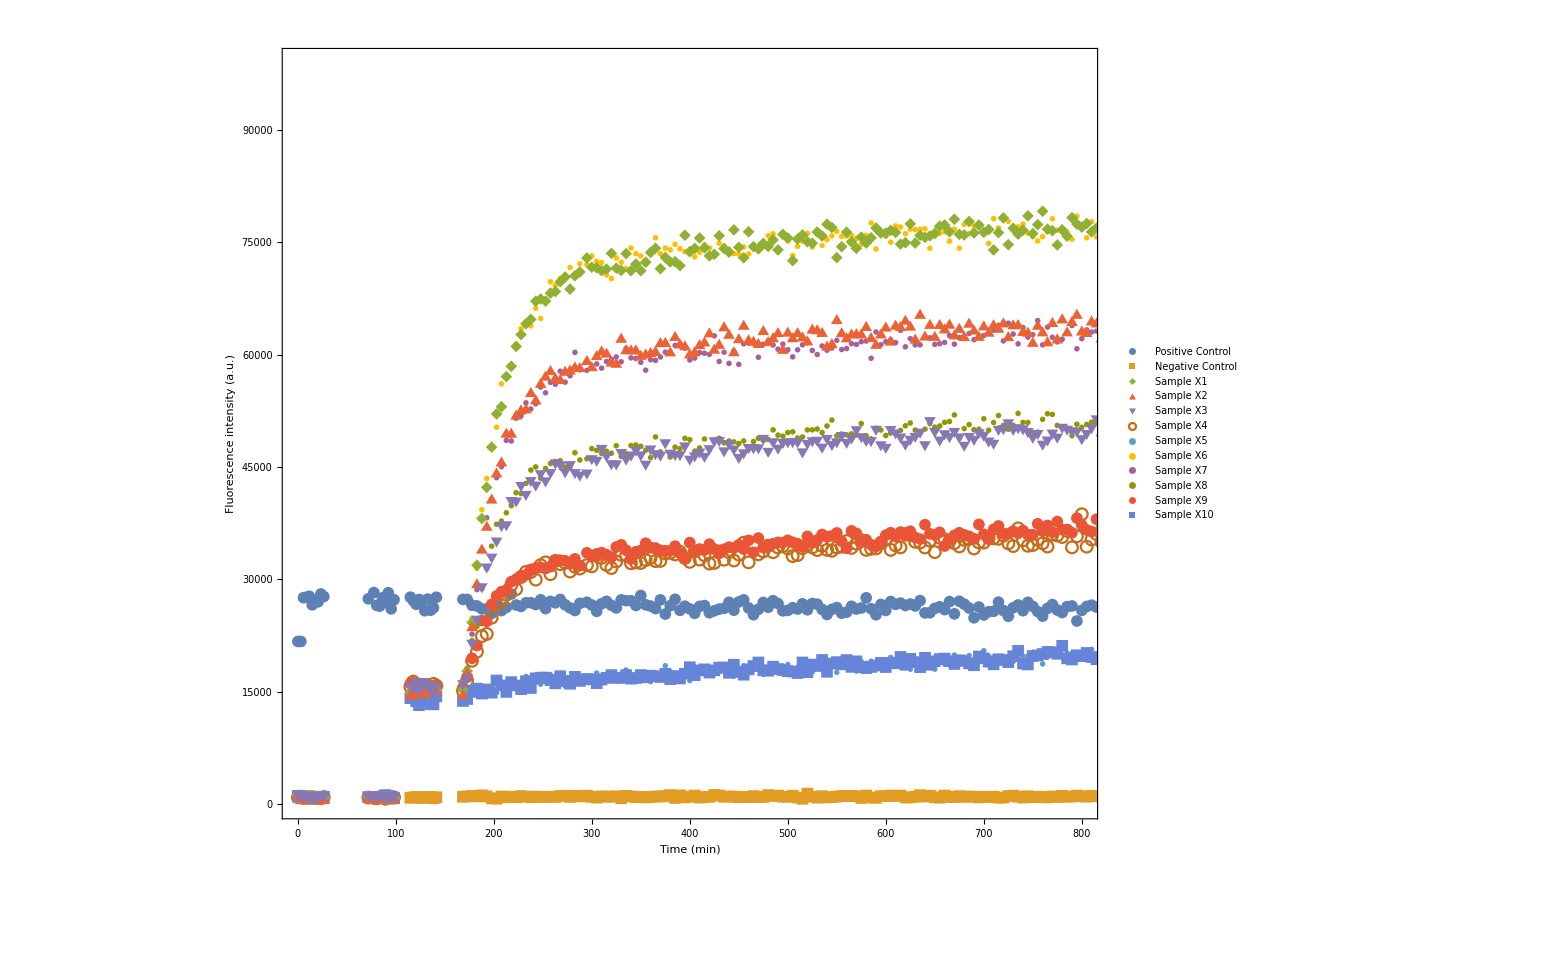

SI\TR_Alexa_raw.pdf

```mathematica
siz=10;
fntsz=35;
list={12,23,24,25,26,27,28,29,30,31,32,33}
concV={"Positive Control","Negative Control","Sample X1","Sample X2","Sample X3","Sample X4","Sample X5","Sample X6","Sample X7","Sample X8","Sample X9","Sample X10"}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnew[[list]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz],Style[concV[[6]],FontSize->fntsz,Thickness[0.1]],Style[concV[[7]],FontSize->fntsz,Thickness[0.1]],Style[concV[[8]],FontSize->fntsz,Thickness[0.1]],Style[concV[[9]],FontSize->fntsz,Thickness[0.1]],Style[concV[[10]],FontSize->fntsz,Thickness[0.1]],Style[concV[[11]],FontSize->fntsz,Thickness[0.1]],Style[concV[[12]],FontSize->fntsz,Thickness[0.1]]},LegendLayout->{"Column",1}],Joined->False,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,12},PlotRange->{{0,800},All}]
Export["SI\\TR_Alexa_raw.pdf",qs]
```

{12,23,24,25,26,27,28,29,30,31,32,33}

{Positive Control,Negative Control,Sample X1,Sample X2,Sample X3,Sample X4,Sample X5,Sample X6,Sample X7,Sample X8,Sample X9,Sample X10}

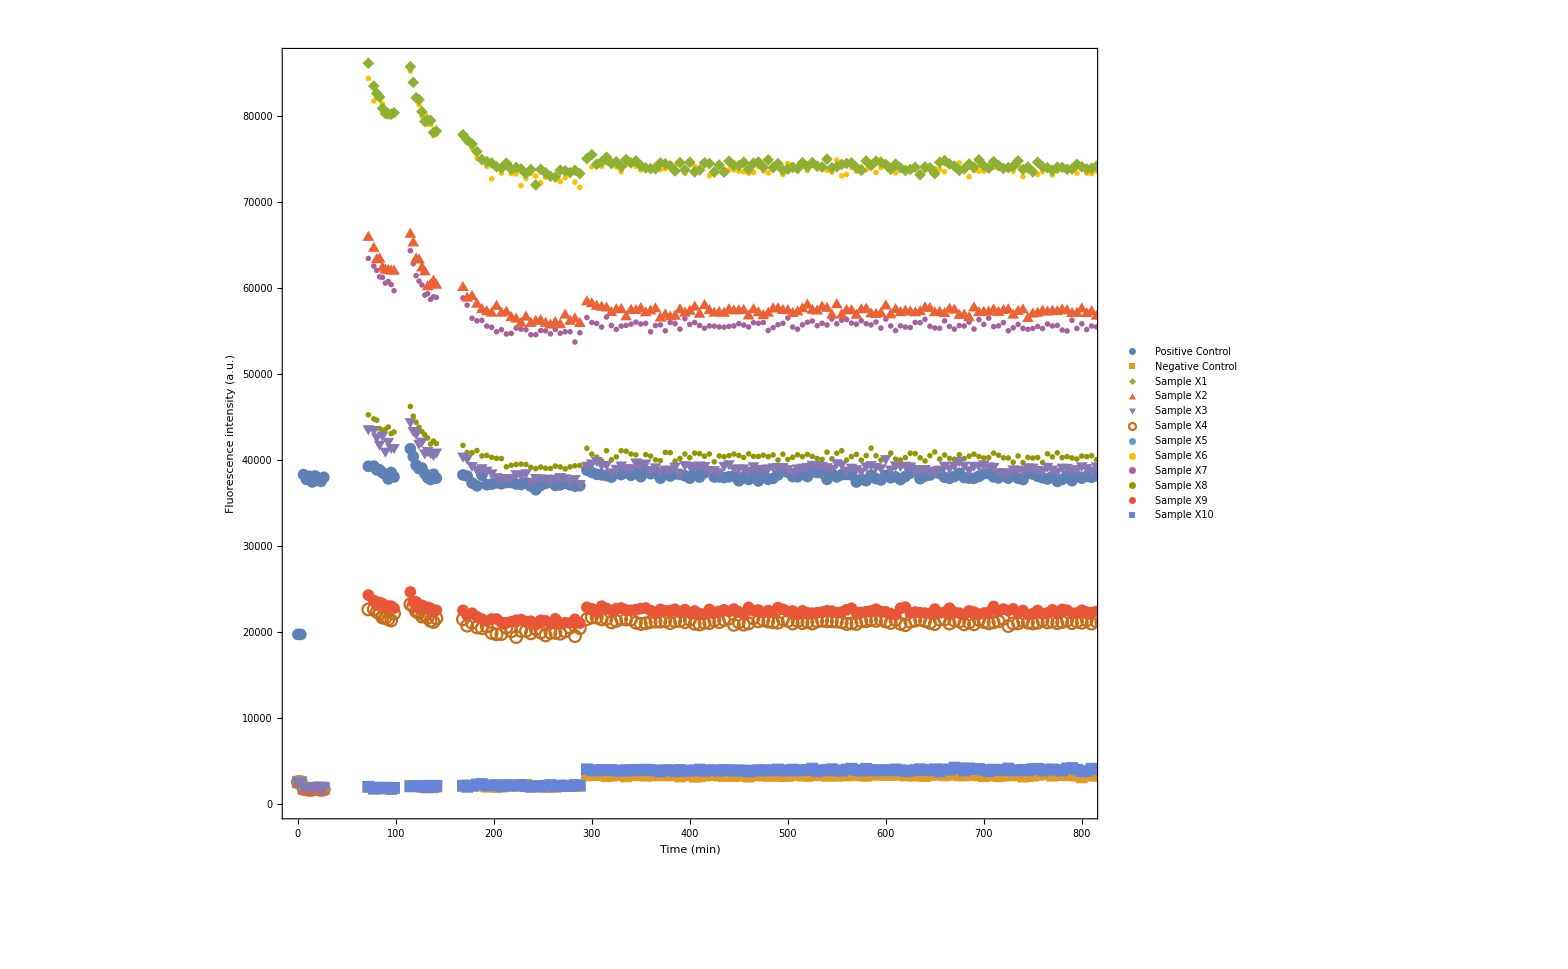

SI\TR_Cy3_raw.pdf

```mathematica
siz=10;
fntsz=35;
list={12,23,24,25,26,27,28,29,30,31,32,33}
concV={"Positive Control","Negative Control","Sample X1","Sample X2","Sample X3","Sample X4","Sample X5","Sample X6","Sample X7","Sample X8","Sample X9","Sample X10"}
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[dnewtem[[list]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[6]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[7]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[8]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[9]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[10]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[11]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[12]],AbsolutePointSize[siz]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz],Style[concV[[6]],FontSize->fntsz,Thickness[0.1]],Style[concV[[7]],FontSize->fntsz,Thickness[0.1]],Style[concV[[8]],FontSize->fntsz,Thickness[0.1]],Style[concV[[9]],FontSize->fntsz,Thickness[0.1]],Style[concV[[10]],FontSize->fntsz,Thickness[0.1]],Style[concV[[11]],FontSize->fntsz,Thickness[0.1]],Style[concV[[12]],FontSize->fntsz,Thickness[0.1]]},LegendLayout->{"Column",1}],Joined->False,PlotStyle->{FontSize->40},PlotMarkers->{Automatic,12},PlotRange->{{0,800},All}]
Export["SI\\TR_Cy3_raw.pdf",qs]
```

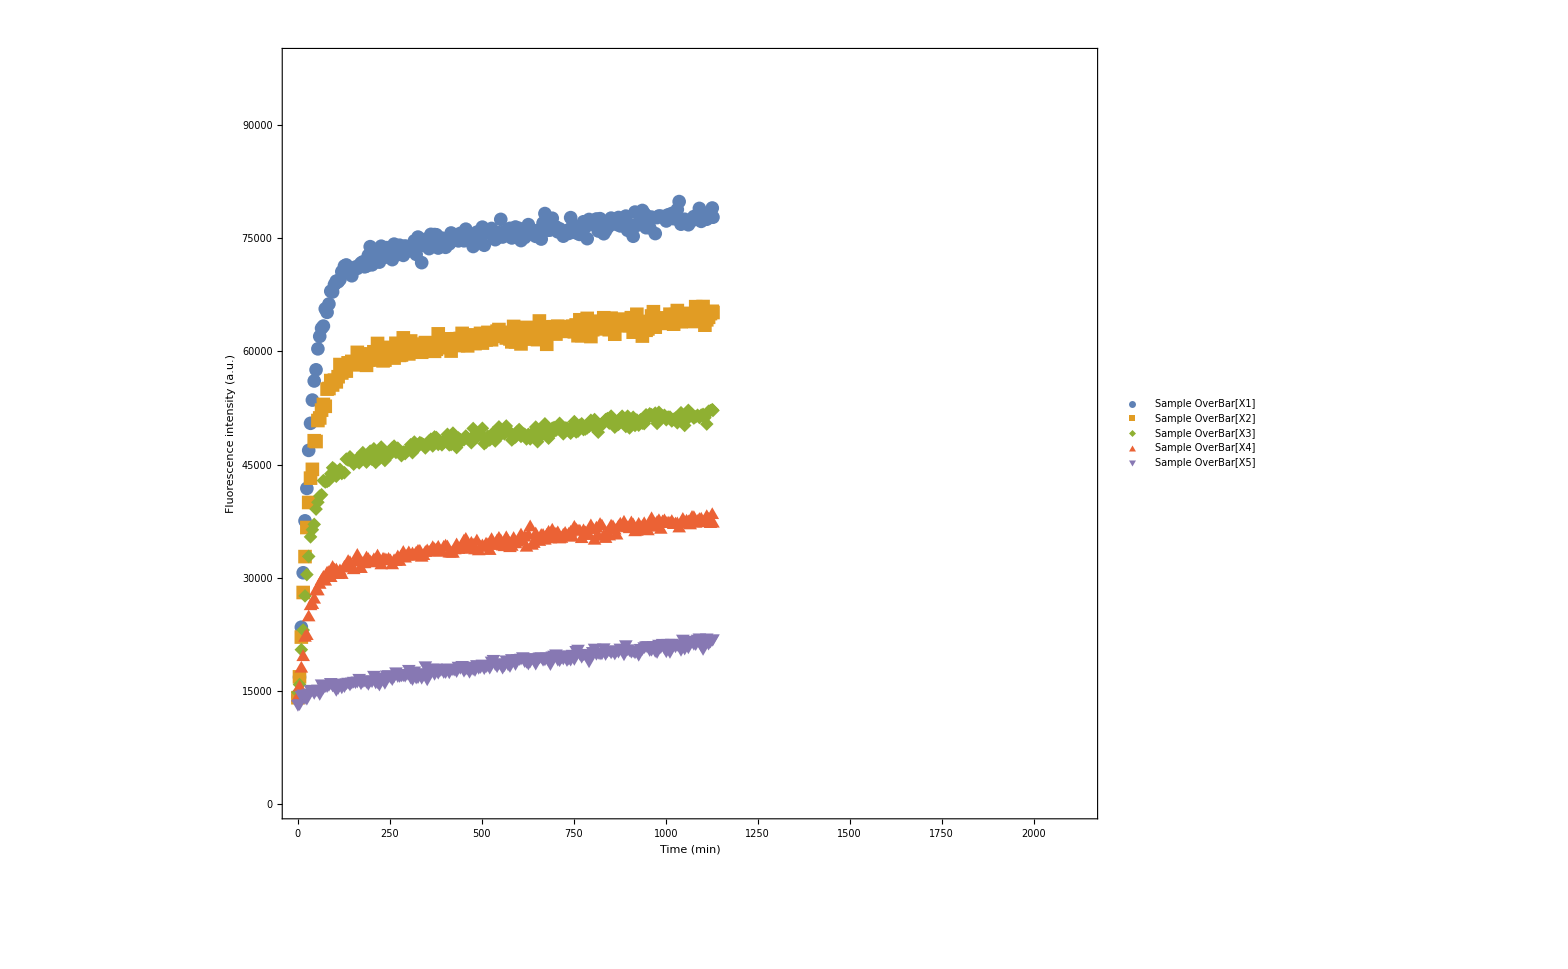

SI\TR_Alexa_norm.pdf

```mathematica
mean[x_]:=
(a1=x[[1;;5]];
For[i=1,i<=5,i++,
For[j=1,j<=Length[x[[i]]],j++,
a1[[i]][[j]][[1]]=x[[i]][[j]][[1]];
a1[[i]][[j]][[2]]=(x[[i]][[j]][[2]]+x[[i+5]][[j]][[2]])*0.5
]];
Return[a1];
)
siz=40;
fntsz=45;

concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[mean[datanormA[[21;;30]]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14}]
Export["SI\\TR_Alexa_norm.pdf",qs]
```

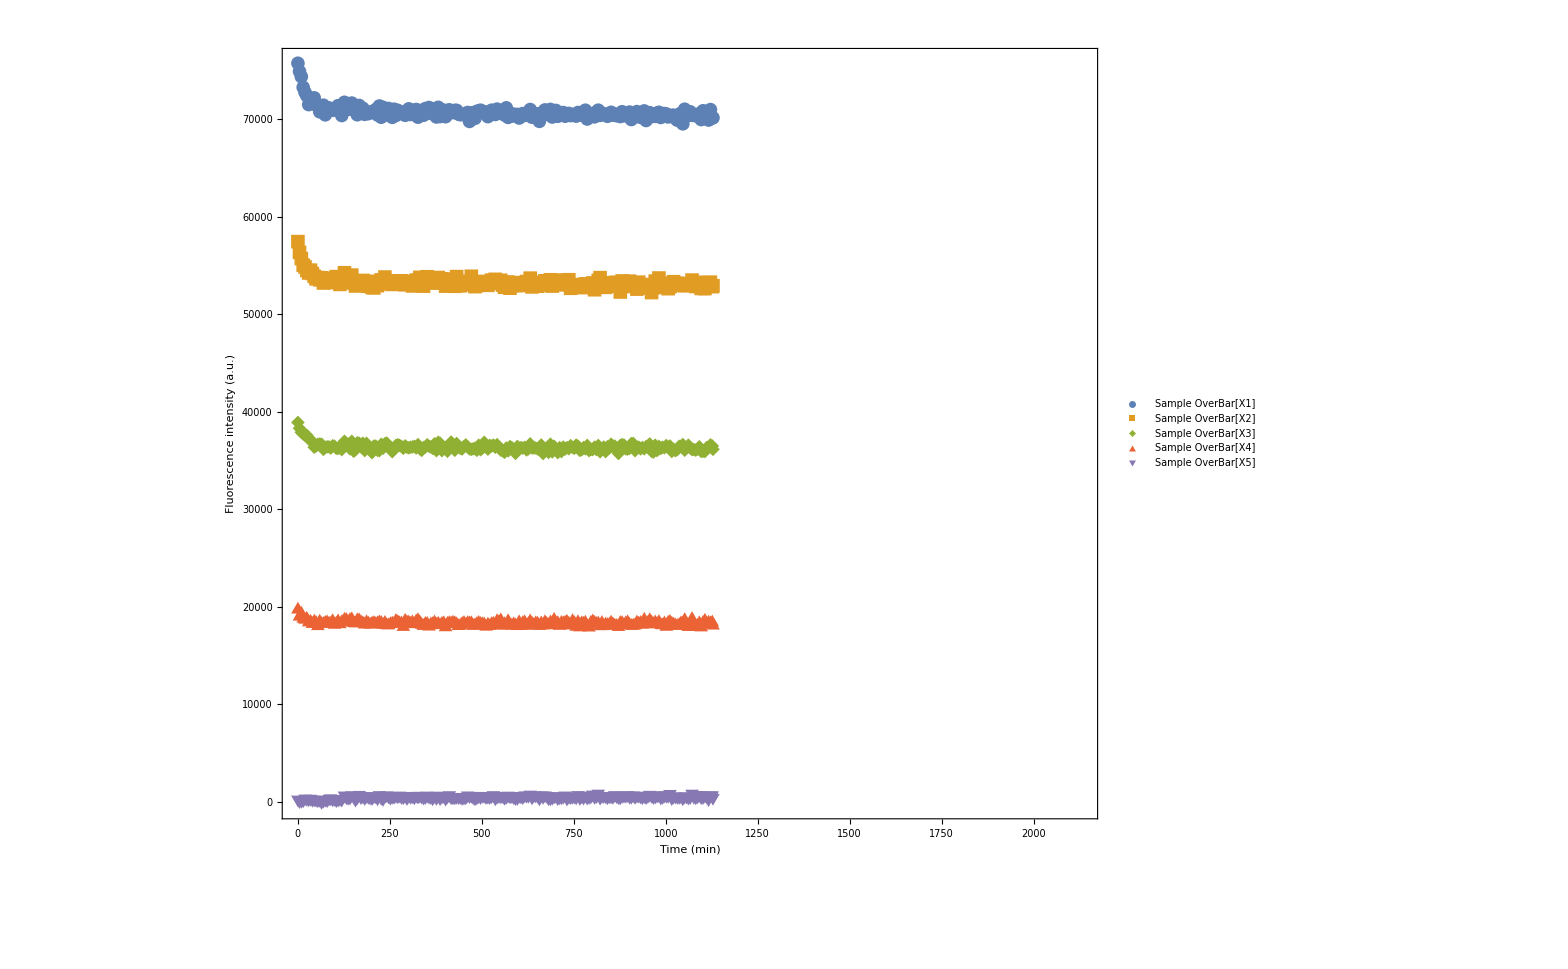

SI\TR_Cy3_norm.pdf

```mathematica
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[mean[datanormC[[21;;30]]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluorescence intensity (a.u.)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14}]
Export["SI\\TR_Cy3_norm.pdf",qs]
```

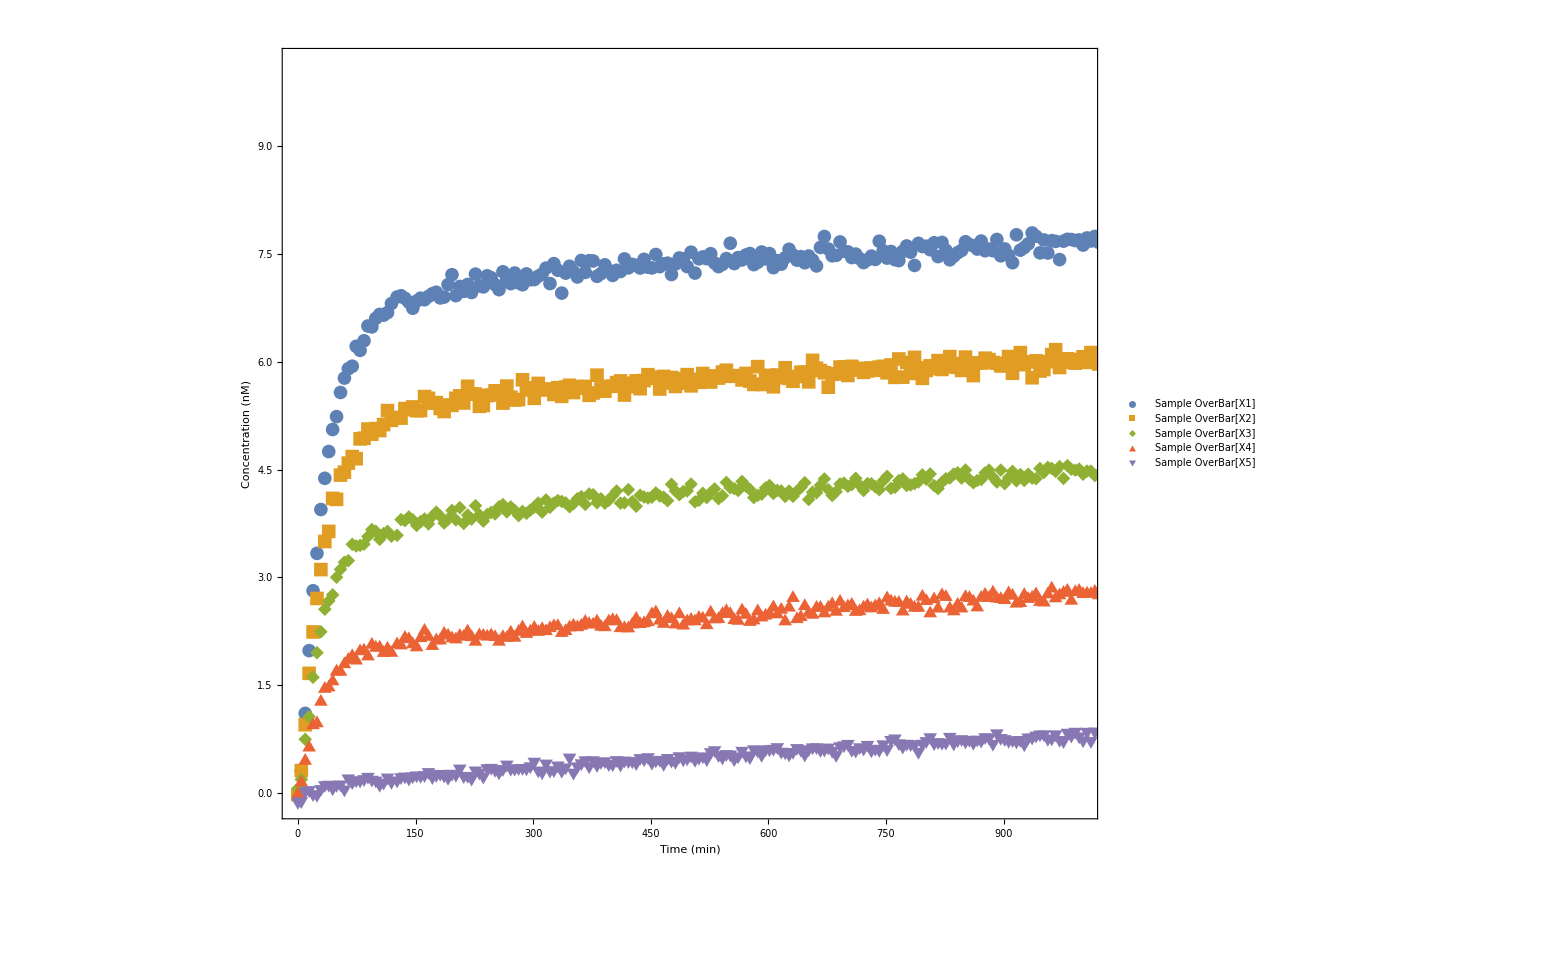

SI\TR_Alexa_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[emp2[[11;;15]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\TR_Alexa_conc.pdf",qs]
```

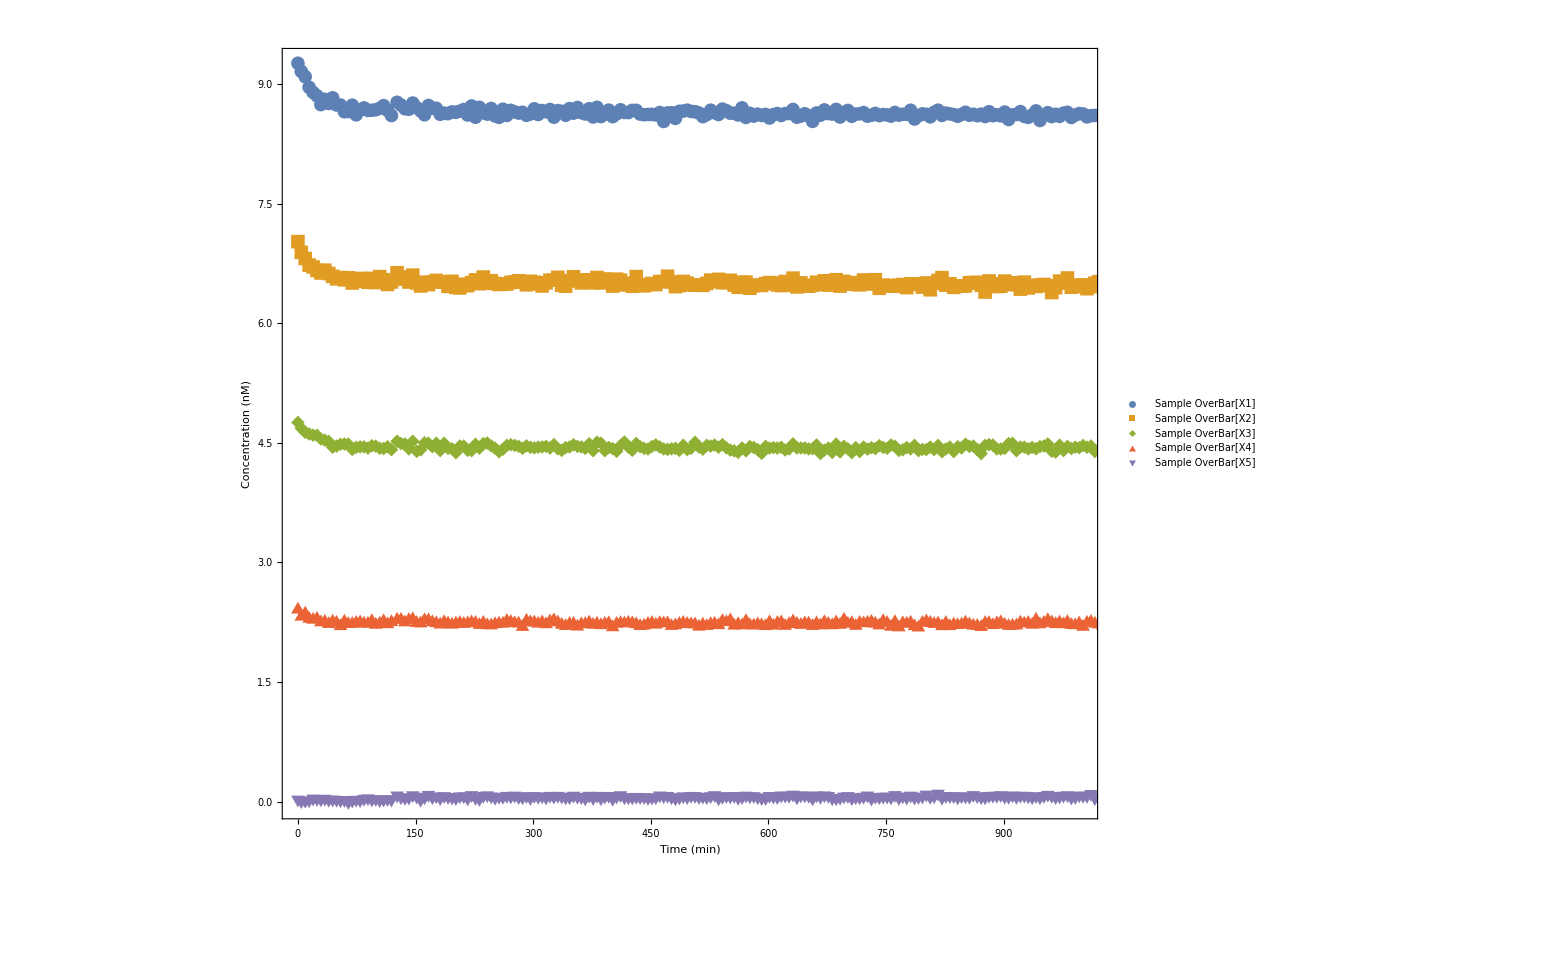

SI\TR_Cy3_conc.pdf

```mathematica
siz=40;
fntsz=45;
concV={"Sample OverBar[X1]","Sample OverBar[X2]","Sample OverBar[X3]","Sample OverBar[X4]","Sample OverBar[X5]"};
SetDirectory[ParentDirectory[NotebookDirectory[]]];
qs=ListPlot[emp[[11;;15]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->45,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]]],Directive[ColorData[97,"ColorList"][[2]]],Directive[ColorData[97,"ColorList"][[3]]],Directive[ColorData[97,"ColorList"][[4]]],Directive[ColorData[97,"ColorList"][[5]]]},{Style[concV[[1]],FontSize->fntsz,Thickness[0.1]],Style[concV[[2]],FontSize->fntsz],Style[concV[[3]],FontSize->fntsz],Style[concV[[4]],FontSize->fntsz],Style[concV[[5]],FontSize->fntsz]},LegendLayout->{"Column",1}],Joined->True,PlotStyle->{FontSize->60},PlotMarkers->{Automatic, 14},PlotRange->{{0,1000},All}]
Export["SI\\TR_Cy3_conc.pdf",qs]
```

```mathematica
conc={6,4,2,1,0};
fs=50;
qs=ListPlot[plotdata[[1;;5]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Fluoroscence intensity (a.u.)"},BaseStyle->fs,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[5]],AbsolutePointSize[siz]]},{Style[ToString[NumberForm[conc[[1]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[2]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[3]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[4]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[5]],3]]<>"nM MT",FontSize->fs]}]];
Export["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\SI\\Template Recovery(fl)_Alexa.pdf",qs]
qs=ListPlot[emp[[1;;5]],Joined->False,Frame->True,FrameLabel->{"Time (min)","Concentration (nM)"},BaseStyle->fs,ImageSize->2000,PlotLegends->PointLegend[{Directive[ColorData[97,"ColorList"][[1]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[2]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[3]],AbsolutePointSize[siz]],Directive[ColorData[97,"ColorList"][[4]],AbsolutePointSize[siz]]},{Style[ToString[NumberForm[conc[[1]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[2]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[3]],3]]<>"nM MT",FontSize->fs],Style[ToString[NumberForm[conc[[4]],3]]<>"nM MT",FontSize->fs]
,Style[ToString[NumberForm[conc[[5]],3]]<>"nM MT",FontSize->fs]}]];
Export["C:\\Users\\asengar\\My Drive\\Ubuntu\\Rakesh\\SI\\Template Recovery(conc)_Alexa.pdf",qs]
```

Part::take: Cannot take positions 1 through 5 in plotdata.

Part::pkspec1: The expression False cannot be used as a part specification.

ListPlot::lpn: plotdata⟦1;;5⟧ is not a list of numbers or pairs of numbers.

C:\Users\asengar\My Drive\Ubuntu\Rakesh\SI\Template Recovery(fl)_Alexa.pdf

C:\Users\asengar\My Drive\Ubuntu\Rakesh\SI\Template Recovery(conc)_Alexa.pdf